```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Cos[2 π x]^3/(1+10 x^4 Cos[π x]^4)
```

```mathematica
v[x_]:=u'[x]
```

```mathematica
u[x]//FullSimplify
```

Cos[2 π x]^3/(1+10 x^4 Cos[π x]^4)

```mathematica
v[x]//FullSimplify
```

(Cos[2 π x]^2 (40 x^3 Cos[π x]^3 Cos[2 π x] (-Cos[π x]+π x Sin[π x])-6 π (1+10 x^4 Cos[π x]^4) Sin[2 π x]))/((1+10 x^4 Cos[π x]^4)^2)

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/third_order_pde/solution/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

5.44327×10^-8

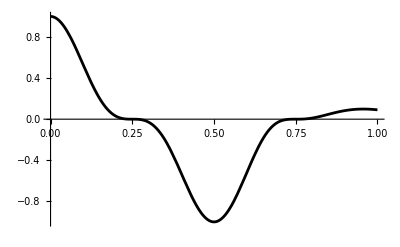

```mathematica
plotuexact=Plot[u[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

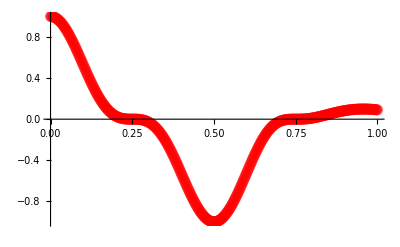

```mathematica
plotunum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

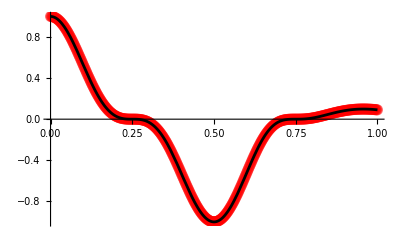

```mathematica
Show[plotunum,plotuexact]
```

```mathematica
(*check for v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/third_order_pde/solution/v.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-v[t[[i,1]]]],{i,1,Length[t]}]]
```

8.24021×10^-8

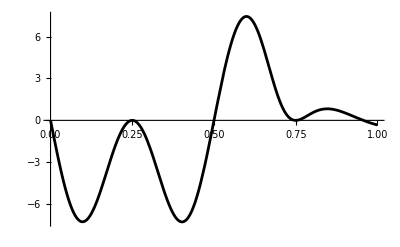

```mathematica
plotvexact=Plot[v[x],{x,xl,xr},PlotRange->Full,PlotStyle->Black]
```

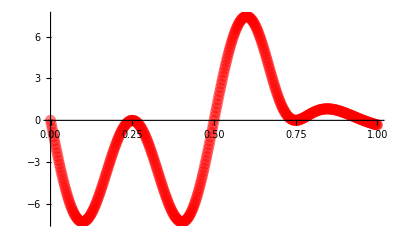

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.5],PointSize->0.02}]
```

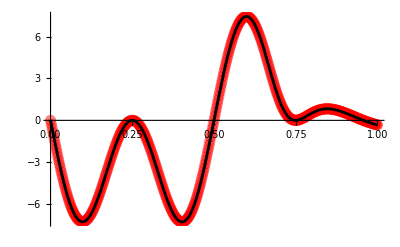

```mathematica
Show[plotvnum,plotvexact]
```